## Dunaev Viktor, 3 kurs, 6 group, 23 variant

## Pre - Task

```mathematica
Needs["UserFunctions`",NotebookDirectory[]<>"UserFunctions.m"]
```

```mathematica
fname = NotebookDirectory[]<>"input.txt"
```

C:\6_Cemestr\DS_Laguto\input.txt

```mathematica
stream = OpenRead[fname]
```

InputStream[…]

```mathematica
vertexNum = Read[stream, {Word, Number}]⟦2⟧
```

6

```mathematica
edgesNum =Read[stream, {Word, Number}]⟦2⟧
```

12

```mathematica
edges =Table[#⟦1⟧->#⟦2⟧&[ToExpression[Read[stream]]],edgesNum]
```

{1->5,2->5,3->1,3->4,3->5,4->1,4->2,4->6,5->4,6->2,6->3,6->5}

```mathematica
vertex = Table[i,{i,1,vertexNum}]
```

{1,2,3,4,5,6}

```mathematica
weight = Range[vertexNum]
```

{1,2,3,4,5,6}

```mathematica
Table[(pos =First[StringCases[#⟦1⟧,x:NumberString:>ToExpression[x]]];val = #⟦2⟧;weight⟦pos⟧ = val)&[Read[stream, {Word, Number}]],vertexNum]
```

{7,4,-1,-7,-2,-1}

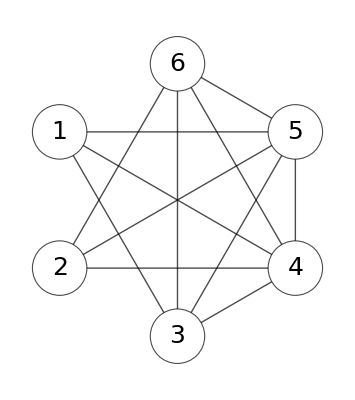

```mathematica
g = GetGraph[vertex,edges]
```

```mathematica
startNode = RandomChoice[vertex]
```

2

```mathematica
dirs= Table[0,Length[vertex]]
```

{0,0,0,0,0,0}

```mathematica
pred = Table[0, Length[vertex]]
```

{0,0,0,0,0,0}

```mathematica
depth = Table[0 , Length[vertex]]
```

{0,0,0,0,0,0}

```mathematica
dinast = {}
```

{}

```mathematica
{tree,graphTree}= Flatten[
Reap[
DepthFirstScan[
UndirectedGraph@g,startNode,{"FrontierEdge"->((edge =#/.(x_<->y_)->(x->y); Sow[edge,RT];If[MemberQ[edges,edge],dirs⟦#⟦2⟧⟧=1;
Sow[edge,ST],dirs⟦#⟦2⟧⟧=-1;Sow[Reverse[edge],ST]];pred⟦#⟦2⟧⟧=#⟦1⟧;depth⟦#⟦2⟧⟧ = depth⟦#⟦1⟧⟧+1)&),"PrevisitVertex"->((AppendTo[dinast,#])&)}],{RT,ST}]⟦2⟧,1]
```

{{2->4,4->3,3->6,6->5,5->1},{4->2,3->4,6->3,6->5,1->5}}

```mathematica
tree
```

{2->4,4->3,3->6,6->5,5->1}

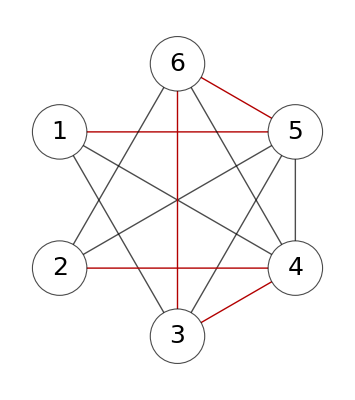

```mathematica
HighlightGraph[g,graphTree]
```

```mathematica
dirs
```

{-1,0,-1,-1,1,-1}

```mathematica
pred
```

{5,0,4,2,6,3}

```mathematica
dinast
```

{2,4,3,6,5,1}

```mathematica
depth
```

{5,0,2,1,4,3}

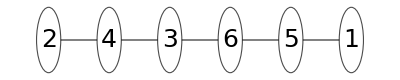

```mathematica
Graph[tree, VertexSize->Large, VertexStyle->White, VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Black,Italic,25], GraphLayout->{"RadialEmbedding"},EdgeShapeFunction->"Arrow", EdgeStyle->Black]
```

```mathematica
TableForm[{vertex,pred,depth, dirs},TableHeadings->{{"Вершины","Список предков","Список глубин", "Список направлений"}}]
```

Вершины | 1 | 2 | 3 | 4 | 5 | 6
Список предков | 5 | 0 | 4 | 2 | 6 | 3
Список глубин | 5 | 0 | 2 | 1 | 4 | 3
Список направлений | -1 | 0 | -1 | -1 | 1 | -1

## Task 1

```mathematica
(*    1) Построить общее решение системы уравнений баланса.
2) Этапы решения (рисунки,таблицы,текст,БЕЗ КОДА) вывести в отдельный pdf файл (см.пример в лекции 6).
  3) Функции пользователя (чтение данных из файла,построение системы,построение частного решения,построение характеристических векторов,общее решение) вынести в отдельный пакет расширения (пакет пользователя).Пакет подключить к основной программе и вызывать функции из пакета.(Можно объединить этапы решения в одну функцию и вызывать ее из пакета для получения общего решения по заданным данным и файла с результатами/этапами решения).*)
```

#### Любое частное решение системы.

```mathematica
pSol = PSolution[vertex,edges,dinast,dirs,pred,weight]
```

{(x̃)_(1,5)→7,(x̃)_(2,5)→0,(x̃)_(3,1)→0,(x̃)_(3,4)→3,(x̃)_(3,5)→0,(x̃)_(4,1)→0,(x̃)_(4,2)→-4,(x̃)_(4,6)→0,(x̃)_(5,4)→0,(x̃)_(6,2)→0,(x̃)_(6,3)→4,(x̃)_(6,5)→-5}

```mathematica
Compile
```

Compile

```mathematica
sys=((Total[Join[Select[edges,MatchQ[#->_]],-Select[edges,MatchQ[_->#]]]]& /@vertex/.(a_->b_)->Subscript[x̃, a,b])⟦#⟧==weight⟦#⟧)&/@vertex
```

{(x̃)_(1,5)-(x̃)_(3,1)-(x̃)_(4,1)==7,(x̃)_(2,5)-(x̃)_(4,2)-(x̃)_(6,2)==4,(x̃)_(3,1)+(x̃)_(3,4)+(x̃)_(3,5)-(x̃)_(6,3)==-1,-(x̃)_(3,4)+(x̃)_(4,1)+(x̃)_(4,2)+(x̃)_(4,6)-(x̃)_(5,4)==-7,-(x̃)_(1,5)-(x̃)_(2,5)-(x̃)_(3,5)+(x̃)_(5,4)-(x̃)_(6,5)==-2,-(x̃)_(4,6)+(x̃)_(6,2)+(x̃)_(6,3)+(x̃)_(6,5)==-1}

```mathematica
sys/.pSol
```

{True,True,True,True,True,True}

#### Общее решение.

```mathematica
Un=Select[edges,Not[MemberQ[graphTree,#]]&]
```

{2->5,3->1,3->5,4->1,4->6,5->4,6->2}

```mathematica
Ut=graphTree
```

{4->2,3->4,6->3,6->5,1->5}

```mathematica
table = Table[0,Length[Un],edgesNum];
```

```mathematica
deltas = GSolution[edges,depth,dirs,pred,Ut,Un]
```

{δ_(2,5)^(2->5)→1,δ_(3,1)^(2->5)→0,δ_(3,5)^(2->5)→0,δ_(4,1)^(2->5)→0,δ_(4,6)^(2->5)→0,δ_(5,4)^(2->5)→0,δ_(6,2)^(2->5)→0,δ_(4,2)^(2->5)→1,δ_(3,4)^(2->5)→1,δ_(6,3)^(2->5)→1,δ_(6,5)^(2->5)→-1,δ_(1,5)^(2->5)→0,δ_(2,5)^(3->1)→0,δ_(3,1)^(3->1)→1,δ_(3,5)^(3->1)→0,δ_(4,1)^(3->1)→0,δ_(4,6)^(3->1)→0,δ_(5,4)^(3->1)→0,δ_(6,2)^(3->1)→0,δ_(4,2)^(3->1)→0,δ_(3,4)^(3->1)→0,δ_(6,3)^(3->1)→1,δ_(6,5)^(3->1)→-1,δ_(1,5)^(3->1)→1,δ_(2,5)^(3->5)→0,δ_(3,1)^(3->5)→0,δ_(3,5)^(3->5)→1,δ_(4,1)^(3->5)→0,δ_(4,6)^(3->5)→0,δ_(5,4)^(3->5)→0,δ_(6,2)^(3->5)→0,δ_(4,2)^(3->5)→0,δ_(3,4)^(3->5)→0,δ_(6,3)^(3->5)→1,δ_(6,5)^(3->5)→-1,δ_(1,5)^(3->5)→0,δ_(2,5)^(4->1)→0,δ_(3,1)^(4->1)→0,δ_(3,5)^(4->1)→0,δ_(4,1)^(4->1)→1,δ_(4,6)^(4->1)→0,δ_(5,4)^(4->1)→0,δ_(6,2)^(4->1)→0,δ_(4,2)^(4->1)→0,δ_(3,4)^(4->1)→1,δ_(6,3)^(4->1)→1,δ_(6,5)^(4->1)→-1,δ_(1,5)^(4->1)→1,δ_(2,5)^(4->6)→0,δ_(3,1)^(4->6)→0,δ_(3,5)^(4->6)→0,δ_(4,1)^(4->6)→0,δ_(4,6)^(4->6)→1,δ_(5,4)^(4->6)→0,δ_(6,2)^(4->6)→0,δ_(4,2)^(4->6)→0,δ_(3,4)^(4->6)→1,δ_(6,3)^(4->6)→1,δ_(6,5)^(4->6)→0,δ_(1,5)^(4->6)→0,δ_(2,5)^(5->4)→0,δ_(3,1)^(5->4)→0,δ_(3,5)^(5->4)→0,δ_(4,1)^(5->4)→0,δ_(4,6)^(5->4)→0,δ_(5,4)^(5->4)→1,δ_(6,2)^(5->4)→0,δ_(4,2)^(5->4)→0,δ_(3,4)^(5->4)→-1,δ_(6,3)^(5->4)→-1,δ_(6,5)^(5->4)→1,δ_(1,5)^(5->4)→0,δ_(2,5)^(6->2)→0,δ_(3,1)^(6->2)→0,δ_(3,5)^(6->2)→0,δ_(4,1)^(6->2)→0,δ_(4,6)^(6->2)→0,δ_(5,4)^(6->2)→0,δ_(6,2)^(6->2)→1,δ_(4,2)^(6->2)→-1,δ_(3,4)^(6->2)→-1,δ_(6,3)^(6->2)→-1,δ_(6,5)^(6->2)→0,δ_(1,5)^(6->2)→0}

```mathematica
gSol = BalanceSolve[deltas,pSol,Ut,Un]
```

{x_(4,2)→-4+x_(2,5)-x_(6,2),x_(3,4)→3+x_(2,5)+x_(4,1)+x_(4,6)-x_(5,4)-x_(6,2),x_(6,3)→4+x_(2,5)+x_(3,1)+x_(3,5)+x_(4,1)+x_(4,6)-x_(5,4)-x_(6,2),x_(6,5)→-5-x_(2,5)-x_(3,1)-x_(3,5)-x_(4,1)+x_(5,4),x_(1,5)→7+x_(3,1)+x_(4,1)}

```mathematica
sys=((Total[Join[Select[edges,MatchQ[#->_]],-Select[edges,MatchQ[_->#]]]]& /@vertex/.(a_->b_)->Subscript[x, a,b])⟦#⟧==weight⟦#⟧)&/@vertex
```

{x_(1,5)-x_(3,1)-x_(4,1)==7,x_(2,5)-x_(4,2)-x_(6,2)==4,x_(3,1)+x_(3,4)+x_(3,5)-x_(6,3)==-1,-x_(3,4)+x_(4,1)+x_(4,2)+x_(4,6)-x_(5,4)==-7,-x_(1,5)-x_(2,5)-x_(3,5)+x_(5,4)-x_(6,5)==-2,-x_(4,6)+x_(6,2)+x_(6,3)+x_(6,5)==-1}

```mathematica
sys/.gSol
```

{True,True,True,True,True,True}